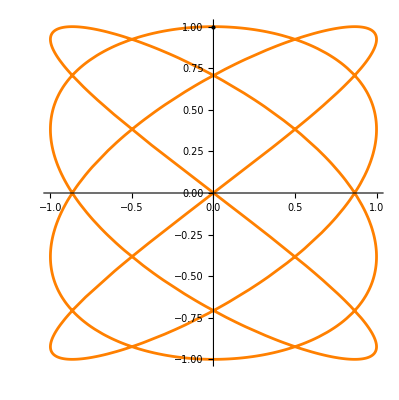

```mathematica
Show[
ParametricPlot[{Sin[4θ],Cos[3θ]},{θ,0,2π},PlotStyle->Orange],
Graphics[Point[{0,1}]]
]
```

```mathematica
ClearAll[θ];
D[{Sin[4θ],Cos[3θ]},{θ,1}].D[{Sin[4θ],Cos[3θ]},{θ,2}]
```

```mathematica
27 Cos[3 θ] Sin[3 θ]-64 Cos[4 θ] Sin[4 θ]
```

27 Cos[3 θ] Sin[3 θ]-64 Cos[4 θ] Sin[4 θ]

```mathematica
Norm[D[{Sin[4θ],Cos[3θ]},{θ,1}]]/.θ->0
```

4